0.930335+0.000138851 x+2.97543×10^-8 x^2

27.0486-0.00708939 x+3.76175×10^-7 x^2

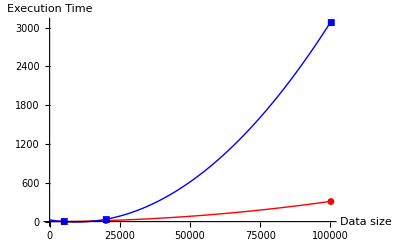

```mathematica
NList={{50*100,2.368444},{200*100,15.60905},{1000*100,312.3580}};
MList={{50*100,1.006071},{200*100,35.73071},{1000*100,3079.855}};
Nfit=Fit[NList,{1,x,x^2},x]
Mfit=Fit[MList,{1,x,x^2},x]
Show[Plot[{Nfit,Mfit},{x,0,100000},PlotStyle->{{Red,Thick},{Blue,Thick}}],ListPlot[{NList,MList},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotMarkers->Automatic],AxesOrigin->{0,0},AxesLabel->{"Data size","Execution Time"}]
```

7.26724×10^-8+7.49942×10^-9 x-2.42235×10^-15 x^2

-1.04232×10^-6+7.54706×10^-9 x-8.23015×10^-16 x^2

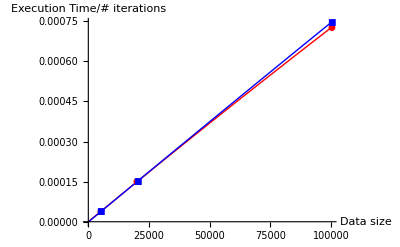

```mathematica
NList={{50*100,2.368444/63143},{200*100,15.60905/104694},{1000*100,312.3580/430369}};
MList={{50*100,1.006071/27434},{200*100,35.73071/238890},{1000*100,3079.855/4131628}};
Nfit=Fit[NList,{1,x,x^2},x]
Mfit=Fit[MList,{1,x,x^2},x]
Show[Plot[{Nfit,Mfit},{x,0,100000},PlotStyle->{{Red,Thick},{Blue,Thick}}],ListPlot[{NList,MList},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotMarkers->Automatic],AxesOrigin->{0,0},AxesLabel->{"Data size","Execution Time/# iterations"}]
```

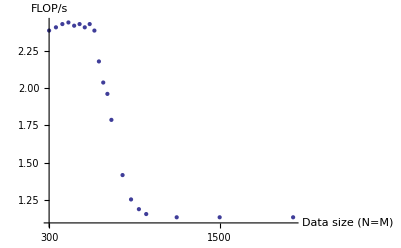

```mathematica
FlopList={{300,2.20*13/12},{320,2.22*13/12},{340,2.24*13/12},{360,2.25*13/12},{380,2.23*13/12},{400,2.24*13/12},{420,2.22*13/12},{440,2.24*13/12},{460,2.20*13/12},{480,2.01*13/12},{500,1.88*13/12},{520,1.81*13/12},{540,1.65*13/12},{600,1.31*13/12},{650,1.16*13/12},{700,1.10*13/12},{750,1.07*13/12},{1000,1.05*13/12},{1500,1.05*13/12},{3000,1.05*13/12}};
ListLogLinearPlot[FlopList,PlotMarkers->None,AxesLabel->{"Data size (N=M)","FLOP/s"},AxesOrigin->{300,1.1}]
```